# Half Rod, Albedo Problem, Isotropic Scattering

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

/Users/eug/Documents/research/hitchhikersscatter

## Exponential Random Flight

## Notation

α - single-scattering albedo
Σt - extinction coefficient
x - position coordinate in rod (source at x = 0)

## Analytic solutions

### Half rod albedo

```mathematica
halfrodAlbedoIsotropic[α_]:=2(-α/2-√(1-α)+1)/α
```

### ‘Radiance’

```mathematica
LR[x_,α_,Σt_]:=ⅇ^(-√(1-α) Σt x)
```

```mathematica
LL[x_,α_,Σt_]:=(α Exp[-Σt √(1-α)x])/(-α+2 √(1-α)+2)
```

### Fluence

```mathematica
ϕ[x_,α_,Σt_]:=LR[x,α,Σt]+LL[x,α,Σt]
```

```mathematica
ϕm[α_,Σt_,k_]:=(2 (1-α)^(-1-k/2) (-1+√(1-α)+α) Σt^(-1-k) Gamma[1+k])/α
```

## load MC data

```mathematica
ppoints[xs_,dx_,maxx_,Σt_]:=Table[{dx(i-1)+0.5dx,(1/Σt)xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
fs=FileNames["code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp*"]
```

{code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.1_mut1.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.1_mut3.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.3_mut1.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.3_mut3.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.5_mut1.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.5_mut3.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.7_mut1.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.7_mut3.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.95_mut1.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.95_mut3.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.98_mut1.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.98_mut3.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.999_mut1.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.999_mut3.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.99_mut1.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.99_mut3.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.9_mut1.0.txt,code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp_c0.9_mut3.0.txt}

## Halfrod Albedo

```mathematica
MCalbedo[f_]:=Module[{data,α},
data=Import[f,"Table"];
α=data[[2,3]];
{α,data[[3,3]]}
]
```

```mathematica
MCalbedos=Table[MCalbedo[f],{f,fs}]
```

{{0.1,0.0262874},{0.1,0.0262874},{0.3,0.0888128},{0.3,0.0888128},{0.5,0.17156},{0.5,0.17156},{0.7,0.291991},{0.7,0.291991},{0.95,0.633904},{0.95,0.633904},{0.98,0.751703},{0.98,0.751703},{0.999,0.938793},{0.999,0.938793},{0.99,0.818082},{0.99,0.818082},{0.9,0.519448},{0.9,0.519448}}

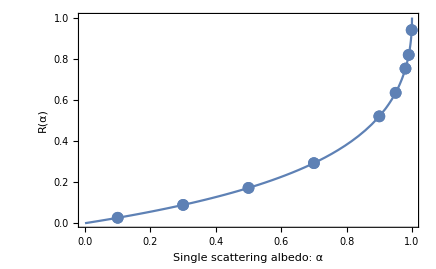

```mathematica
Clear[α];vizrodalbedoiso=Show[
Plot[halfrodAlbedoIsotropic[c],{c,0,1}],
ListPlot[MCalbedos]
,Frame->True,FrameLabel->{{R[α],},{"Single scattering albedo: α","Total Reflectance/Albedo R(α): isotropically-scattering half rod"}}
]
```

## Compare Deterministic and MC

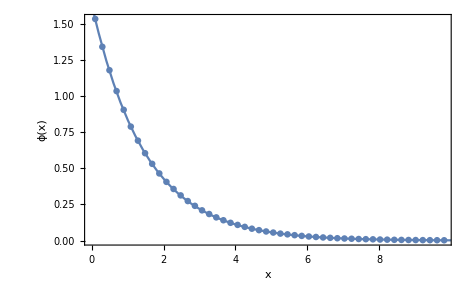

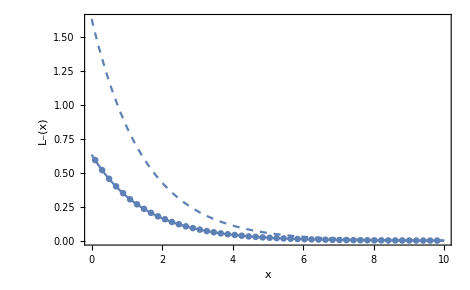

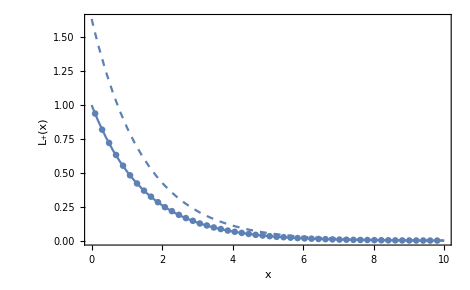

```mathematica
filename=fs[[10]];
data=Import[filename,"Table"];
Σt=data[[1,11]];
α=data[[2,3]];
maxx=data[[2,5]];
dx=data[[2,7]];
numcollorders=data[[2,11]];
nummoments=data[[2,13]];

densmom=data[[11]];

pointsCL = data[[7]];
(* divide by Σt to convert collision density into L *)
plotpointsCL=ppoints[pointsCL,dx,maxx,Σt];
pointsCR = data[[9]];
plotpointsCR=ppoints[pointsCR,dx,maxx,Σt];
(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=ppoints[pointsCL+pointsCR,dx,maxx,Σt];

plotϕ=Show[
ListPlot[plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕ[x,α,Σt],{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x],},{x,"Semi-infinite rod, albedo problem, isotropic scattering, fluence ϕ[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}}
]

plotLL=Show[
ListPlot[plotpointsCL,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LL[x,α,Σt],{x,0,maxx},PlotRange->All],
Plot[ϕ[x,α,Σt],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubMinus[L][x],},{x,"Semi-infinite rod, albedo problem, isotropic scattering, L_-[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]

plotLR=Show[
ListPlot[plotpointsCR,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LR[x,α,Σt],{x,0,maxx},PlotRange->All],
Plot[ϕ[x,α,Σt],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubPlus[L][x],},{x,"Semi-infinite rod, albedo problem, isotropic scattering, L_+[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]
```

### Compare moments of ϕ

Divide these results, which are collision density moments, by Σt to produce radiance/fluence moments:

```mathematica
ϕmoments=N[{data[[11]]}/Σt];
ks={Table[k,{k,0,nummoments-1}]};
analytic=Table[ϕm[α,Σt,k],{k,ks}];
j=Join[ks,analytic,ϕmoments];
TableForm[
Join[{{"k","analytic","MC"}},Transpose[j]]
]
```

k | analytic | MC
0 | 2.43659 | 2.44266
1 | 3.63225 | 3.64293
2 | 10.8293 | 10.8351
3 | 48.43 | 48.0367
4 | 288.781 | 280.723
5 | 2152.44 | 2014.66
6 | 19252. | 16933.9
7 | 200895. | 161081.
8 | 2.39581×10^6 | 1.68986×10^6
9 | 3.21432×10^7 | 1.9167×10^7

### N-th order Radiance/Angular flux

ⅇ^(-3 x) x (0.0634742+x (0.190423+x (0.244829+(0.163219+0.0489658 x) x)))

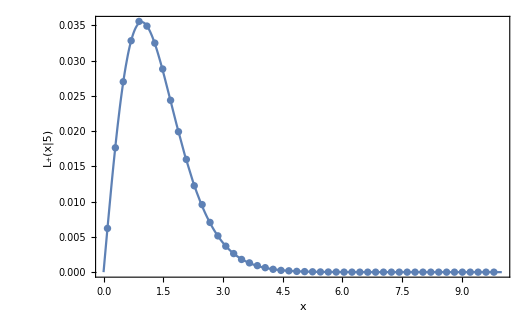

```mathematica
nthL=data[[13+numcollorders+1;;13+2numcollorders]];
nthR=data[[13+2 numcollorders+2;;-1]];

(* choose order:*)
n=5;

Clear[c];LnR=FullSimplify[SeriesCoefficient[LR[x,c,Σt],{c,0,n}] α^n]
plotLnp=Show[
ListPlot[ppoints[nthR[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LnR,{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{SubPlus[L]["x|"<>ToString[n]],},{x,"Semi-Infinite Rod, albedo problem, isotropic scattering, L_+[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]
```

### N-th order Fluence / scalar flux

ⅇ^(-3 x) (0.0317371+x (0.190423+x (0.380845+x (0.380845+(0.204024+0.0489658 x) x))))

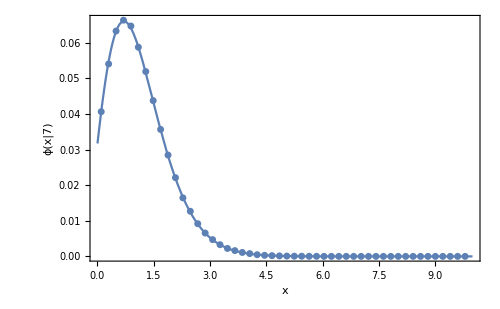

```mathematica
(* choose order:*)
n=5;

Clear[c];
phin=FullSimplify[SeriesCoefficient[ϕ[x,c,Σt],{c,0,n}] α^n]
plotphin=Show[
ListPlot[ppoints[nthR[[n+1]]+nthL[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[phin,{x,0,maxx},PlotRange->All]
,Frame->True,ImageSize->500,
FrameLabel->{{ϕ["x|7"],},{x,"Semi-Infinite Rod, isotropic point, isotropic scattering, ϕ[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]
```